# CoffeeCode Mathematica

CoffeeCode Mathematica Interface, © 2019 Johannes Bausch
For joint Graph State project with Felix Leditzky

This file can be exported as a module, and then imported in a script.

# CoffeeCode Interface

## Setup [Build paths to be fixed here; contains more instructions]

### Paths and Unicorns

These lines HAVE TO BE MODIFIED.

Edit scripts/make-build-dir.sh to activate a valid build environment for building with a modern gcc (>8.2). You can remove all the conda... blabla lines there if the compilation environment is installed globally anyhow. The options you pass to cmake there have to match those that you would pick when setting up a solver directory manually with ccmake. This also includes setting the paths for the boost and nauty libraries (via the options -D PATH_BOOST=/path/to/boost -D PATH_NAUTY=/path/to/nauty).

```mathematica
Clear[CurrentDir]
CurrentDir:=If[$InputFileName≠"",DirectoryName[$InputFileName],NotebookDirectory[]]
```

```mathematica
(* fix paths in this file *)
Get["CCInterfacePaths.m",Path->CurrentDir];
```

Path to precompiled full solvers: C:\Users\Johannes\Programmieren\C++\CoffeeCode\CoffeeCode/build/release_full/

Path to precompiled full solvers for all channels: C:\Users\Johannes\Programmieren\C++\CoffeeCode\CoffeeCode/build/release_full_arbch/

Path to create parallel solver subdirectories: C:\Users\Johannes\Programmieren\C++\CoffeeCode\CoffeeCode/build/

Script how to setup new parallel solver subdirectories: C:\Users\Johannes\Programmieren\C++\CoffeeCode\CoffeeCode\scripts\/make-build-dir.sh

Results path, can be used as RESULTSPATH (can be ignored): C:\Users\Johannes/Desktop/GraphStateResults/

```mathematica
(* execute this cell to open the build script for manual editing *)
SystemDialogInput["FileOpen",PARALLELBUILDSETUPSCRIPT]
```

### Build Environments

```mathematica
On[Assert];(* enable sanity checks instead of failing silently *)
```

```mathematica
(* avoid race conditions when building in parallel *)
Clear[ParallelBuildDirectory]
ParallelBuildDirectory[]:=Module[{
targetFolder=PARALLELBUILDPATH<>"release-"<>ToString@$SessionID<>"."<>ToString@$KernelID<>"/"
},
If[!DirectoryQ[targetFolder],
Echo["setting up parallel build directory: "<>targetFolder];
RunProcess[{PARALLELBUILDSETUPSCRIPT,targetFolder}] (* bug with commands like "source" *)
];
targetFolder
]
```

```mathematica
ParallelBuildDirectory[]
```

```mathematica
Clear[BuglessRunProcess]
BuglessRunProcess[exec_String,what_,input_String:"",opts:OptionsPattern[]]:=Module[{
process=StartProcess[exec,opts],
out
},
If[input≠"",WriteLine[process,input]];
While[ProcessStatus[process,"Running"],Pause[1]];
out=ReadString[process];
<|
"ExitCode"->ProcessInformation[process]["ExitCode"],
"StandardError"->"",
"StandardOutput"->out
|>
]

Unprotect[StringForm];
StringForm[a_,b_Parallel`Kernels`kernel]:=""
```

## Basic Graph Functionality [install IGraphM once below, then forget]

### IGraphM

Uncomment the last line in the following cell, then execute to install IGraphM. This only has to be done once per machine.

```mathematica
updateIGraphM[]:=Module[{json,download,target,msg},Check[json=Import["https://api.github.com/repos/szhorvat/IGraphM/releases","JSON"];
download=Lookup[First@Lookup[First[json],"assets"],"browser_download_url"];
msg="Downloading IGraph/M "<>Lookup[First[json],"tag_name"]<>" ...";
target=FileNameJoin[{CreateDirectory[],"IGraphM.paclet"}];
If[$Notebooks,PrintTemporary@Labeled[ProgressIndicator[Appearance->"Necklace"],msg,Right],Print[msg]];
URLSave[download,target],Return[$Failed]];
If[FileExistsQ[target],PacletManager`PacletInstall[target],$Failed]]
(*updateIGraphM[]*) (* uncomment this once and run to install IGraphM locally, then comment again *)
```

```mathematica
Needs["IGraphM`"]
ParallelNeeds["IGraphM`"];
```

### Group for Graph State

GroupForGraph gives the full automorphism group of the underlying graph; we color the environment vertices in a different color to make sure the permutation group will be a product across this partitioning.

```mathematica
Clear[GroupForGraph]
GroupForGraph[graph_Graph,kSys_Integer,extraStabilizedVertices_List:{}]:=GroupForGraph[graph,kSys,extraStabilizedVertices]=With[{
kTot=VertexCount@graph,
(* {1,3,11} for a graph of size 14 would be mapped to {1,0,2,0,0,0,0,0,0,0,3,0,0,0} *)
extraColors=Normal@SparseArray[Thread[extraStabilizedVertices->Range@Length@extraStabilizedVertices],VertexCount@graph]
},
IGBlissAutomorphismGroup[{graph,"VertexColors"->ConstantArray[0,kSys]~Join~ConstantArray[kTot^2,kTot-kSys]+extraColors}]
]
```

```mathematica
GroupForGraph[StarGraph[10],9]
```

```mathematica
(* for iterating over tuples, we'll only need the system vertices RestrictGroup, not the full group *)
```

```mathematica
Clear[RestrictGroup]
RestrictGroup[group_PermutationGroup,kSys_Integer]:=RestrictGroup[group,kSys]=group/.{p_Integer/;p>kSys->Nothing}/.Cycles[{}]->Nothing
```

### Plot Environment Vertices in Red

```mathematica
Clear[EnvironmentPlot]
EnvironmentPlot[g_Graph,systemSize_,vl_:None]:=Graph[g,VertexStyle->(
Thread[VertexList[g]⟦-(VertexCount@g-systemSize);;⟧->Red]
),VertexSize->.2,VertexLabels->vl]
```

### Create all Possible Choices of Hairs to the Environment

```mathematica
Clear[IsomorphicHairChoiceQ,HairColoring]
HairColoring[hairs_]:=HairColoring[Sort@hairs]=Length/@GroupBy[hairs,Identity]
IsomorphicHairChoiceQ[g_Graph,hairs1_,hairs2_]:=IsomorphicHairChoiceQ[g,hairs1,hairs2]=IsomorphicHairChoiceQ[g,hairs2,hairs1]=IGBlissIsomorphicQ[
{g,"VertexColors"->HairColoring@hairs1},
{g,"VertexColors"->HairColoring@hairs2}
]
IsomorphicHairChoiceQ[g_Graph]:=IsomorphicHairChoiceQ[g,#1,#2]&
```

```mathematica
Clear[HairGraph,AllHairGraphs]
HairGraph[g_Graph,hairs_]:=HairGraph[g,hairs]=With[{
new=VertexCount@g+Range@Length@hairs
},
EdgeList[g]~Join~Thread[hairs<->new]//Graph
]
AllHairGraphs[g_Graph,generator_:Hold[Subsets[#]⟦2;;⟧&]]:=AllHairGraphs[g,generator]=With[{
(* first check for graph isomorphism using a vertex coloring *)
uniqueHairEndpoints=DeleteDuplicates[
ReleaseHold[generator][VertexList@g],
IsomorphicHairChoiceQ[g]
]
},
EnvironmentPlot[HairGraph[g,#],VertexCount@g]&/@uniqueHairEndpoints
]
```

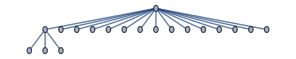
```mathematica
AllHairGraphs[-Graphics-,Subsets[#,{1}]&]
```

### Detecting Products of Symmetric Groups

```mathematica
Clear[ProductOfSymmetricGroupsQ]
ProductOfSymmetricGroupsQ[group_PermutationGroup]:=With[{
orbits=GroupOrbits@group
},
(GroupOrder/@(
GroupStabilizer[group,Complement[Flatten@orbits,#]]&/@orbits
)
)==(Factorial/@Length/@orbits)
]
```

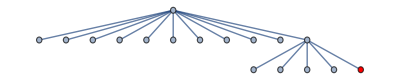
```mathematica
GroupForGraph[-Graphics-,16]
ProductOfSymmetricGroupsQ@%
GroupOrbits@%%
```

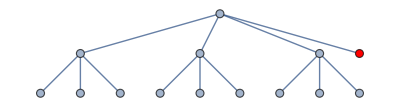
```mathematica
GroupForGraph[-Graphics-,13]
ProductOfSymmetricGroupsQ@%
```

```mathematica
Clear[CanonicalizeByOrbits]
(* sort graph vertices such that environment all the way to the right, and orbits of size > 1 come up first *)
CanonicalizeByOrbits[graph_Graph,kSys_Integer,extraStabilizedVertices_List:{}]:=With[{
orbits=GroupOrbits[GroupForGraph[graph,kSys,extraStabilizedVertices],Range@VertexCount@graph],
kTot=VertexCount@graph
},

With[{
coloring=Thread/@MapIndexed[Function[{orbit,i},
(* environment last, length 1 next, nontrivial orbits first; stable sort so add i *)
If[Min@orbit>kSys,
orbit->10kTot+First@i,
If[Length@orbit==1,
orbit->5kTot+First@i,
orbit->First@i
]]
],orbits]//Flatten//SortBy[First]
},
Graph[
IGBlissCanonicalGraph[{graph,"VertexColors"->Last/@coloring}],
VertexLabels->"Index"
]
]
]
```

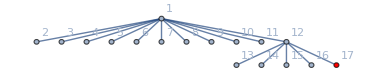
```mathematica
CanonicalizeByOrbits[-Graphics-,16]
```

### Detecting Multiple Hairs per Orbit

```mathematica
Clear[OrbitsHaveMultipleHairsQ]
OrbitsHaveMultipleHairsQ[group_PermutationGroup,g_Graph,kSys_Integer]:=Module[{
environmentVertices=VertexList[g]⟦kSys+1;;⟧,
hairNeighbourIndices
},
hairNeighbourIndices=VertexIndex[g,#]&/@VertexList@Subgraph[NeighborhoodGraph[g,environmentVertices],Complement[VertexList@g,environmentVertices]];

Intersection[#,hairNeighbourIndices]&/@GroupOrbits[group]//AnyTrue[#,Length@##>1&]&
]
```

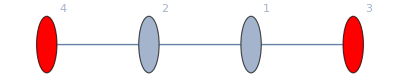
```mathematica
-Graphics-
RestrictGroup[GroupForGraph[%,2],2]
OrbitsHaveMultipleHairsQ[%,%%,2]
```

## CoffeeCode Link [See individual sections for tests]

```mathematica
CCCUSTOMINSTANCEFILE="cc-instance-custom.h";
```

### Exporting MM symbols

```mathematica
Clear[ExportAdjacencyMatrix]
ExportAdjacencyMatrix[g_Graph]:=With[{
Avec=g//AdjacencyMatrix//Normal//Flatten
},
StringJoin[ToString/@Avec]
]
```

```mathematica
(* for the trivial transversal we simply pass an orbit, sort the graph canonically etc *)
Clear[TrivialSGSTransversalMMForm]
TrivialSGSTransversalMMForm[list_List,kSys_Integer]:=With[{
orbits=list/.{n_Integer}:>Nothing//SortBy[First]
},
With[{
lengths=Accumulate[Length/@orbits]
},
With[{
orbitBounds={0}~Join~lengths//Partition[#,2,1]&
},

StringRiffle[(
"\tTrivialSGSOrbit<"<>ToString[#1]<>", "<>ToString[#2]<>">"
)&@@@orbitBounds,
",\n"]
]//("using sgs = TrivialSGSTransversal<"<>ToString[kSys]<>",\n"<>#<>"\n>;")&
]
]
```

```mathematica
RestrictGroup[GroupForGraph[-Graphics-,2],2]
TrivialSGSTransversalMMForm[GroupOrbits@%,2]
```

```mathematica
(* we use these two heads to determine the type of variable passed to CoffeeCode *)
Unprotect[Numeric,Exact];Clear[Numeric,Exact];Protect[Numeric,Exact];

Clear[ExportSymmetricCCInstance]
(* we don't re-check pType for validity here, see sanity checks in PauliAction *)
ExportSymmetricCCInstance[graph_Graph,kSys_Integer,pType_,extraStabilizedVertices_List:{},name_:"graphstate_instance"]:=Module[{
group=RestrictGroup[GroupForGraph[graph,kSys,extraStabilizedVertices],kSys]//Echo[#,"group"]&,
kTot=VertexCount@graph,
poly
},

(* pType determines polynomial type used *)
poly=If[StringQ[pType],
If[pType=="Mono",
"using Polynomial = UnivariatePolynomial",
"using Polynomial = MultivariatePolynomial"
],

"constexpr static "<>
If[Length@First@pType==1,
"UnivariateSamples",
"MultivariateSamples"
]<>
"<"<>ToString[Length@pType]<>"> SamplePoints{"<>
ToString[NumberForm[List@@pType,10]]<>
"};\n"<>
"using Polynomial = SampledPolynomial<SamplePoints>"

];

(* pick trivial or nauty solver/iterator *)
If[!OrbitsHaveMultipleHairsQ[group,graph,kSys]∧ProductOfSymmetricGroupsQ@group,
(* write Orbits as expected for TrivialSGS Solver *)
With[{
orbits=GroupOrbits@group,
graphCanonicalized=CanonicalizeByOrbits[graph,kSys,extraStabilizedVertices]
},

If[Length@orbits==0∨Max[Length/@orbits]==1,Echo["WARN: symmetry group is 0. Not a valid symmetric problem instance."];Throw["invalid instance"]
];
Echo["Product symmetry group detected. CanonicalImage=trivial."];

"struct "<>name<>" {\n"<>
TrivialSGSTransversalMMForm[orbits,kSys]<>"\n"<>
"constexpr static size_t k_sys = "<>ToString[kSys]<>", k_env = "<>ToString[kTot-kSys]<>";\n"<>
"constexpr static AdjacencyMatrixT<"<>ToString[kTot]<>"> adjacency_matrix{"<>ToString[Normal@AdjacencyMatrix@graphCanonicalized]<>"};\n"<>
poly<>";\n"<>
"};"
]
,
(* write SGSGenerators as expected for Nauty *)
With[{},
Echo["Nested symmetry group or multiple hairs per orbit detected. CanonicalImage=nauty."];

"struct "<>name<>" {\n"<>
"constexpr static size_t k_sys = "<>ToString[kSys]<>", k_env = "<>ToString[kTot-kSys]<>";\n"<>
"constexpr static AdjacencyMatrixT<"<>ToString[kTot]<>"> adjacency_matrix{"<>ToString[Normal@AdjacencyMatrix@graph]<>"};\n"<>
poly<>";\n"<>
"};"
]
]
]
```

```mathematica
(* numeric sampled polynomial *)
g=Graph[RootedGraphProduct[StarGraph[10],StarGraph[5],{2,3},1],VertexLabels->"Index"]
ExportSymmetricCCInstance[g,VertexCount@g-1,Numeric[{.11111111, .2, .3},{.33, .44, .55},{.1, .2, .3}]]
```

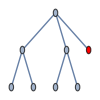
```mathematica
(* can enforce to use the non-nauty symmetric solver by flagging certain vertices as not symmetric *)ExportSymmetricCCInstance[-Graphics-,7,"Mono",{2}]
```

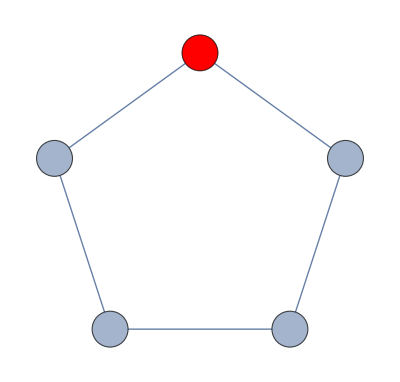
```mathematica
(* multiple hairs per orbit can mean connecting to the same environment vertex. *)
ExportSymmetricCCInstance[-Graphics-,4,"Multi"]
```

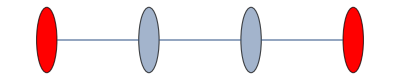
```mathematica
(* it can also mean two different hairs. *)
ExportSymmetricCCInstance[-Graphics-,2,"Mono"]
```

```mathematica
(* we can also numerically sample from this polynomial; easiest is just one value for p=p1=p2=p3 *)
ExportSymmetricCCInstance[-Graphics-,2,Numeric[{.1905}]]
```

```mathematica
(* or multiple samples, but still assuming p1=p2=p3 *)
ExportSymmetricCCInstance[-Graphics-,2,Numeric[{.1904}, {.001}, {.001}]]
```

```mathematica
(* or one sample, but for different ps *)
ExportSymmetricCCInstance[-Graphics-,2,Numeric[{.1904,.1905,.1906}]]
```

### Build Interface

```mathematica
Clear[MakeCC]
MakeCC[kSys_Integer,kEnv_Integer]:=With[{
out=RunProcess[
{
"make",
"-B",
"K_SYS="<>ToString@kSys,
"K_ENV="<>ToString@kEnv
},
ProcessDirectory->ParallelBuildDirectory[]
]
},
If[StringTrim@out["StandardError"]≠"",Echo[out["StandardError"]]];
If[out["ExitCode"]≠0(*∨out["StandardError"]≠""*),Echo[out];Throw["make error"]];
]
MakeCC[graph_Graph,kSys_Integer,pType_,extraStabilizedVertices_List:{}]:=With[{
instanceFileContent=ExportSymmetricCCInstance[graph,kSys,pType,extraStabilizedVertices]
},

Export[ParallelBuildDirectory[]<>CCCUSTOMINSTANCEFILE,instanceFileContent,"Text"];
MakeCC[kSys,VertexCount@graph-kSys]
]
```

```mathematica
(* this fails if the folder for the symmetric solver is not already existent with a valid cc-instance-custom.h: MakeCC[9,1] *)
```

```mathematica
(* try "Mono", "Multi" *)
MakeCC[-Graphics-,7,"Mono"]
```

```mathematica
(* try various numerics as above *)
MakeCC[-Graphics-,7,Numeric[{.1,.11, .12}]]
```

```mathematica
Clear[RunCC]
RunCC[graph_Graph,kSys_Integer,pType_,extraStabilizedVertices:_List:{}]:=With[{},
If[!MakeCC[graph,kSys,pType,extraStabilizedVertices],Return[False]];

With[{
ccResult=BuglessRunProcess["CoffeeCode",All,ProcessDirectory->ParallelBuildDirectory[]]
},
If[ccResult["ExitCode"]≠0∨ccResult["StandardError"]≠"",Echo[ccResult];Throw["run error"]];

Check[
ImportString[ccResult["StandardOutput"],"RawJSON"],
Echo[ccResult];
Throw["import error"]
]
]
]
```

```mathematica
RunCC[-Graphics-,7,Numeric[{.19}],{2}]
```

```mathematica
ExportAdjacencyMatrix[StarGraph[6]]
```

### Full Solver Interface

```mathematica
Clear[CCPath]
CCPath[kSys_Integer,kEnv_Integer,pType_String]:=CCPath[kSys,kEnv,pType]=If[pType=="Mono",CCRELEASEPATHFULLSOLVER,CCRELEASEPATHFULLSOLVERARBCH]<>"CoffeeCode."<>ToString[kSys]<>"."<>ToString[kEnv]

(* RunCC overload *)
RunCC[graph_Graph,kSys_Integer,pType_String,"Full"]:=Module[{
adjacencyMatrix=ExportAdjacencyMatrix@graph,
kEnv=VertexCount@graph-kSys
},
With[{
executable=CCPath[kSys,kEnv,pType]
},

If[!FileExistsQ[executable],
Echo[executable<>" not found"];
Throw["run error"]
];

With[{
ccResult=BuglessRunProcess[executable,All,adjacencyMatrix]
},
If[ccResult["ExitCode"]≠0∨ccResult["StandardError"]≠"",Echo[ccResult];Throw["run error"]];

Check[
ImportString[ccResult["StandardOutput"],"RawJSON"],
Echo[ccResult];
Throw["import error"]
]
]
]
]
```

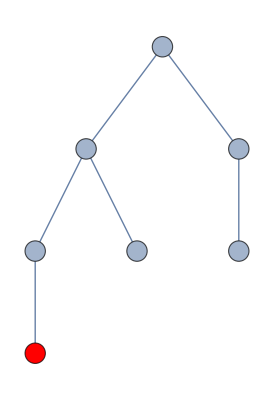
```mathematica
RunCC[-Graphics-,6,"Mono","Full"]
```

```mathematica
RunCC[-Graphics-,6,"Multi","Full"]
```

### Importing JSON format

```mathematica
Clear[CoeffArrayToPoly,MultArrayToPoly]
CoeffArrayToPoly[{q1_,__},{coeffs__Integer}]:=Sum[{coeffs}⟦i⟧ q1^(i-1),{i,1,Length@{coeffs}}]
CoeffArrayToPoly[{q1_,q2_,q3_},{coeffs__List}]:=If[MatchQ[q1,0]∨MatchQ[q2,0]∨MatchQ[q3,0],Module[{qq1,qq2,qq3},
Limit[(#1 qq1^(#2⟦1⟧)qq2^(#2⟦2⟧)qq3^(#2⟦3⟧)),{qq1->q1,qq2->q2,qq3->q3}]
],
(#1 q1^(#2⟦1⟧)q2^(#2⟦2⟧)q3^(#2⟦3⟧))
]&@@@{coeffs}//Total
MultArrayToPoly[{q0_,qs__}]:=Function[{mult,list},If[Length@list==0,Nothing,{
mult,
q0 CoeffArrayToPoly[{qs},list]//Simplify
}]]
```

```mathematica
MultArrayToPoly[{q0,q1,p,q3}]@@@{
{8000,{{1,{1,1,1}},{2,{2,1,1}},{11,{0,0,0}},{3,{15,2,2}}}},
{1300,{{1,{1,1,1}},{2,{2,1,1}},{11,{0,0,0}},{3,{15,2,2}}}},
{10,{}}
}
```

```mathematica
Clear[PauliActionCC]
PauliActionCC[graph_Graph,kSys_Integer,p_,symmetricSolver_:True,extraStabilizedVertices:_List:{}]:=Module[{
kTot=VertexCount@graph,
kEnv=VertexCount@graph-kSys,

pp=If[MatchQ[p,_Exact],
(* either of the form
Exact[p]
Exact[p/3,q/5,1-q,pq]
*)
If[!(Length@p==1∨Length@p==4),
Echo["either one or four symbolic parameters for Exact[...]"];
Throw["wrong Exact format"]
];

(* create list of length four *)
If[Length@p==1,
{1-p⟦1⟧,p⟦1⟧/3,p⟦1⟧/3,p⟦1⟧/3},
List@@p
],

(* or of the form of triples
Numeric[{{.3, .1, .1}, {.2, .2, .15}, ...}]
*)
If[!MatchQ[p,_Numeric],
Echo["either Exact or Numeric p expected"];
Throw["wrong format for p"]
];
If[!symmetricSolver,
Echo["numeric argument for full solver not supported"];
Throw["wrong Numeric argument"]
];

If[Length@p==0,Throw["no sample points given"]];
If[!Equal@@Length/@p,Throw["not all sample points have the same parameter count"]];
If[Length@First@p≠4,Throw["sample points have to be 4-tuples"]];

(* create list of 4-tuples *)
N@List@@p
],
pType,

λ,λa,λm,λma
},


If[kEnv>kSys∨kSys<1∨kTot<2,Throw["invalid params"]];
pType=If[MatchQ[p,_Numeric],
Numeric@@(({#⟦2⟧/#⟦1⟧,#⟦3⟧/#⟦1⟧,#⟦4⟧/#⟦1⟧})&/@pp),
If[Length@p==1,"Mono","Multi"] 
];

(* get lambda and lambda_a *)
With[{
result=If[symmetricSolver,
RunCC[graph,kSys,pType,extraStabilizedVertices],
RunCC[graph,kSys,pType,"Full"]
]
},

If[MatchQ[p,_Numeric],
(* return precalculated values *)
Precalculated[
((First/@pp)^kSys Last@result["lambda"])->First@result["lambda"],
((First/@pp)^kSys Last@result["lambda_a"])-> First@result["lambda_a"]
]
,
(* calculate exact polynomial *)
With[{
toPolyFn=MultArrayToPoly[{pp⟦1⟧^kSys,pp⟦2⟧/pp⟦1⟧,pp⟦3⟧/pp⟦1⟧,pp⟦4⟧/pp⟦1⟧}]
},

{{λm,λ},{λma,λa}}={
toPolyFn@@@result["lambda"]//Transpose,
toPolyFn@@@result["lambda_a"]//Transpose
};

(* final expression in the variables given *)
Thread/@Thread[{λ,λa/2^(kTot-kSys)}->{λm,λma}]
]
]
]
]
```

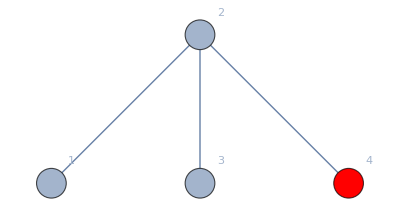
```mathematica
PauliActionCC[-Graphics-,3,Numeric@@Table[N@{1-3p,p,p,p},{p,Range@5/100}]]
```

## User Interface

## Entropy and CI

```mathematica
Clear[ShannonEntropyMult,CIMult]
ShannonEntropyMult[l_List]:=l/.Rule[0,_]:>0/.Rule[term_,mult_]:>-mult*term Log2[term]//Total
CIMult[{λ_,λa_}]:=(ShannonEntropyMult[λa]-ShannonEntropyMult[λ])/Log2@Total@(Last/@List@@λa)
CIMult[Precalculated[λ_->_,λa_->multa_]]:=(λa-λ)/Log2@multa
```

```mathematica
(* finds zero crossings in a list *)
Clear[ZeroCrossings]
ZeroCrossings[l_List]:=Module[{t,u,v},
t={Sign[l],Range[Length[l]]}//Transpose;
u=Select[t,First[#]≠0&];
v=SplitBy[u,First]; 
{Most[Max[#[[All,2]]]&/@v],Rest[Min[#[[All,2]]]&/@v]}//Transpose
]
```

```mathematica
Clear[CIThreshold]
CIThreshold[pa_List,q_Exact,compile_:False]:=Module[{
targetFunction,
var=First@q
},
Assert[Length@q==1∧var==p];

If[!compile,
targetFunction=Function[p,CIMult@pa] (* this scope conflict is intended *)
];

FindRoot[targetFunction[p],
{p,.04,.16},
Method->"Secant",
AccuracyGoal->9,
MaxIterations->1000,
WorkingPrecision->MachinePrecision
]
]

(* this cannot be exact, of course; for now we just numerically interpolate and find roots there; alternatively use ZeroCrossings above *)
CIThreshold[pa_Precalculated,p_Numeric,range_:All,mode_:"FindRoot"]:=Module[{
data=(CIMult@pa)⟦range⟧,
pts=(List@@p)⟦range⟧,
crossings,dataF,ptsF,x
},

If[mode=="ZeroCrossings",
crossings=ZeroCrossings[data];
Between[{pts⟦#1⟧,pts⟦#2⟧}]&@@@crossings,

(* else *)
dataF=Interpolation[data,InterpolationOrder->2];
ptsF=ListInterpolation[#,InterpolationOrder->2]&/@Transpose[pts];

With[{xx=x/.FindRoot[dataF[x],
{x,1,Length@data,1,Length@data},
Method->Automatic,
AccuracyGoal->6,
MaxIterations->1000,
WorkingPrecision->30
]},
#[xx]&/@ptsF
]
]
]

CIThreshold[g_Graph,kSys_Integer,p_,symmetricSolver_:True,extraStabilizedVertices_List:{}]:=With[{
pa=PauliActionCC[g,kSys,p,symmetricSolver,extraStabilizedVertices]
},
CIThreshold[pa,p]
]
```

```mathematica
RootedGraphProduct[StarGraph[2],StarGraph[2],{2},1]
(* for numeric input, the threshold is just a list of points where the function value crosses *)
CIThreshold[%,VertexCount@%-1,Exact[p],False]
```

## Interface Tutorial

### Manual Export

#### Create graphs by hand

To create graphs by hand, look up the following functions:

```mathematica
AdjacencyGraph
SparseArray
PathGraph
```

Or directly use MM’s Graph object, where edges are entered with ESC ue ESC

```mathematica
Graph[{1<->2,3<->4,3<->5,1<->3}]
```

#### Create a random graph, add a hair, and plot.

```mathematica
CompleteGraph[10];
HairGraph[%,{10,9}];
graph=EnvironmentPlot[%,10]
```

#### Export instance

Just adjacency matrix for Full Solver

```mathematica
ExportAdjacencyMatrix[-Graphics-]
```

SGS for Symmetric Solver

```mathematica
ExportSymmetricCCInstance[-Graphics-,16]
```

### Automatic Export, Build and Import

#### Get CI for a Graph

Remove the semicolon to see full analytic expression. If you give “p”, that corresponds to giving CHANNELDEPOLARIZING where all the terms are equal; alternatively you can specify an array of four individual Pauli coefficients, e.g. {1-3 p^2,p^2,p^2,p^2}, or use a predefined block (see section “Entropy and CI” above).

```mathematica
CIMult@@PauliActionCC[-Graphics-,3,p];
```

For plotting, use e.g.

```mathematica
CIMult@@PauliActionCC[-Graphics-,7,p];
Plot[%,{p,0,1}]
```

The same graph is small enough to be faster with the full solver:

```mathematica
CIMult@@PauliActionCC[-Graphics-,7,p,False];
Plot[%,{p,0,1}]
```

If the symmetry group is 0, we cannot solve with the symmetric solvers; an error is thrown that you can catch.

```mathematica
Catch@CIThreshold[-Graphics-,6,p]
```

Solving fully still works.

```mathematica
Catch@CIThreshold[-Graphics-,6,p,False]
```

## Optimization Runs

Everything below can be safely deleted and is not necessary for the CoffeeCode interface. It contains some helpers for graph generation.

### Unique Graph Hash

This graph hash can be used in filenames; it canonicalizes the graph first to ensure that for different isomorphic graphs one gets the same hash.
Note that, in principle, the filename can be decoded to the underlying graph by replacing - with /, Base64-decode, and then ImportString with Graph6 as format.

```mathematica
Clear[GraphHash]
GraphHash[g_Graph,kSys_Integer]:=StringTrim@ExportString[ExportString[CanonicalizeByOrbits[g,kSys],"Graph6"],"Base64"]//StringReplace[#,{"/"->"-"}]&
```

### Rooted Graph Product

```mathematica
Clear[RootedGraphProduct]
RootedGraphProduct[g1_Graph,g2_Graph,v1_Integer,v2_Integer]:=With[{
vcount1=VertexCount@g1,
vertices2=VertexList@g2,
edges2=EdgeList@g2
},
With[{
vmap=If[#==v2,v1,If[#<v2,#+vcount1,#+vcount1-1]]&
},
GraphUnion[g1,Graph[vmap/@vertices2,Map[vmap,edges2,{2}]]]
]
]

RootedGraphProduct[g1_Graph,g2_Graph,v1_List,v2_Integer]:=
Fold[f,{g1,g2,v2},v1]//.f[{gg1_,gg2_,vv2_},vv1_]:>{RootedGraphProduct[gg1,gg2,vv1,vv2],gg2,vv2}//First
```

### Concatenated Graphs

Maybe you want to fill these in?

## Two-Level Tree Graphs

### Graph Generation

```mathematica
Clear[All2LevelGraphs]
(* all 2 level graphs with vertex count < n *)
All2LevelGraphs[n_,segmentSizes_List:{}]:=With[{
partitions=Cases[
IntegerPartitions[n-2,{2,n},If[Length@segmentSizes==0,Range[n],segmentSizes]],
{x_,xs__}/;x≥Length[{xs}]
]
},
With[{
head=StarGraph[First@#+1,VertexLabels->"Index"],
legs=StarGraph[##+1,VertexLabels->"Index"]&/@Rest@#
},
<|
"legcount"->Length@legs,
"graph"->Fold[f,head,{Range@Length@legs+1,legs}ᵀ]//.f[g1_Graph,{i_Integer,g2_Graph}]:>RootedGraphProduct[g1,g2,{i},1]
|>
]&/@partitions
]
```

```mathematica
All2LevelGraphs[14,{3,5,7}]
```

### Numeric Search Run

```mathematica
(* get precomputed sample ranges *)
Get["p_values.m",Path->CurrentDir]
```

```mathematica
(* the parameter is the resoultion *)
SAMPLES["2Pauli"][10]
SAMPLES["depolarizing"][5]
```

```mathematica
(* we can evaluate those points *)
Rest@CHANNELS["2Pauli"]/.p->#&/@SAMPLES["depolarizing"][5]
```

```mathematica
Clear[MultiResolutionSamples]
MultiResolutionSamples[chan_,threshold_,n_:10]:=MultiResolutionSamples[chan]=With[{
coarse=SAMPLES[chan][10],
fine=SAMPLES[chan][100],
ultra=SAMPLES[chan][1000],
ludicrous=SAMPLES[chan][10000]
},
Sort@Union[
coarse,
Nearest[fine,threshold,n],
Nearest[ultra,threshold,n],
Nearest[ludicrous,threshold,n]
]
]
```

```mathematica
MultiResolutionSamples["2Pauli",0.1135]
```

```mathematica
(* we take finer and finer samples around the points of interest where we expect a crossing *)
MultiResolutionSamples["depolarizing",0.1904]
ListLogPlot[Norm[#-0.1904]&/@%]
```